Vektorfelder

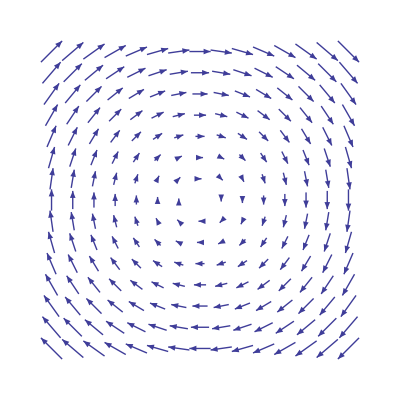

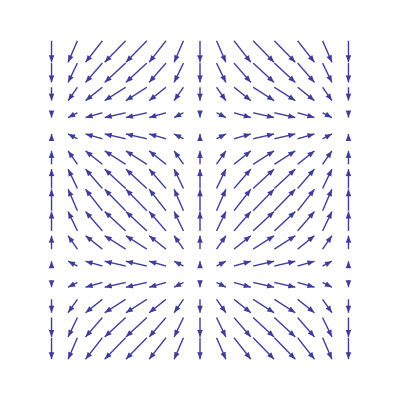

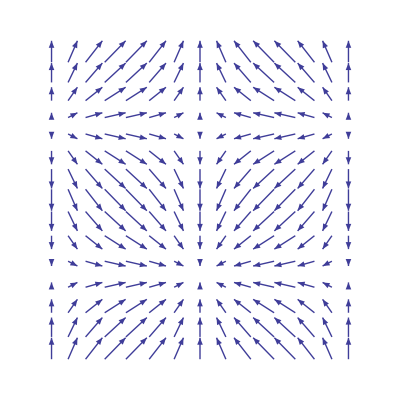

```mathematica
Vektorfelder 

VectorPlot[
{y,-x},
{x,-3,3},
{y,-3,3},
Frame->False]
VectorPlot[
{Sin[x],Cos[y]},
{x,-π,π},
{y,-π,π},
Frame->False]
VectorPlot[
{-Sin[x],-Cos[y]},
{x,-π,π},
{y,-π,π},
Frame->False]
```

```mathematica
Farbkrams
ColorData["Gradients"]
```

{AlpineColors,Aquamarine,ArmyColors,AtlanticColors,AuroraColors,AvocadoColors,BeachColors,BlueGreenYellow,BrassTones,BrightBands,BrownCyanTones,CandyColors,CherryTones,CMYKColors,CoffeeTones,DarkBands,DarkRainbow,DarkTerrain,DeepSeaColors,FallColors,FruitPunchColors,FuchsiaTones,GrayTones,GrayYellowTones,GreenBrownTerrain,GreenPinkTones,IslandColors,LakeColors,LightTemperatureMap,LightTerrain,MintColors,NeonColors,Pastel,PearlColors,PigeonTones,PlumColors,Rainbow,RedBlueTones,RedGreenSplit,RoseColors,RustTones,SandyTerrain,SiennaTones,SolarColors,SouthwestColors,StarryNightColors,SunsetColors,TemperatureMap,ThermometerColors,ValentineTones,WatermelonColors}

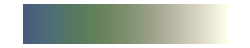
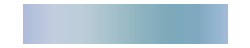
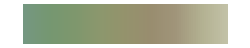
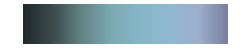
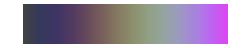
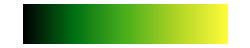
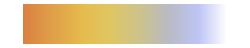
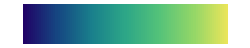

```mathematica
GraphicsGrid[Partition[ColorData[#,"Image"]&/@ColorData["Gradients"],3],ImageSize->300]
```

Skalarfelder

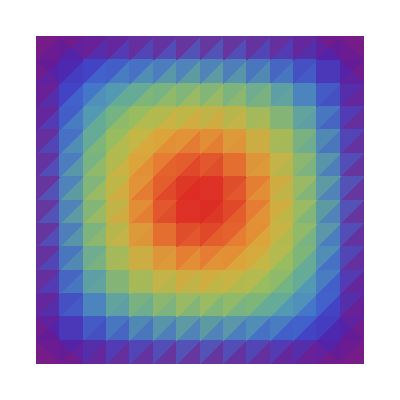

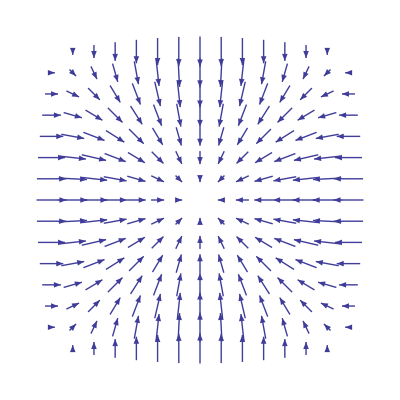

```mathematica
Skalarfelder
(* Skalarfelder *)
plotRange={0,π};
DensityPlot[
Sin[x]Sin[y],
{x,plotRange[[1]],plotRange[[2]]},
{y,plotRange[[1]],plotRange[[2]]},
Frame ->False,
ColorFunction->"Rainbow",
MaxRecursion->5,
PlotPoints->15]
VectorPlot[
{Sin[y]Cos[x],Sin[x]Cos[y]},
{x,plotRange[[1]],plotRange[[2]]},
{y,plotRange[[1]],plotRange[[2]]},
Frame->False]
```